### Set up the code

```mathematica
qn[q1_,n_,α_]:=q1 (1-α)^(n-1)
```

```mathematica
pn[q1_,n_,α_]:=1-qn[q1,n,α]
```

```mathematica
p1=pn[q1,1,α]
```

1-q1

```mathematica
p2=pn[q1,2,α]
```

1-q1 (1-α)

```mathematica
Bin[n_,k_,p_]:=PDF[BinomialDistribution[n,p],k]
```

### Mean matrix

```mathematica
Clear[m]
```

```mathematica
n = 6-2(m )
```

6-2 m

```mathematica
m11=2(m-1)(1-q1)
```

2 (-1+m) (1-q1)

```mathematica
m12=2q1 (1-q1)
```

2 q1-2 q1^2

```mathematica
m13= (1-q1)^2
```

(1-q1)^2

```mathematica
m15=2 n (1-q1)
```

2 (6-2 m) (1-q1)

```mathematica
m21=(m-1)(1-q1(1-α))
```

(-1+m) (1-q1 (1-α))

```mathematica
m24=1-q1(1-α)
```

1-q1 (1-α)

```mathematica
m25=n(1-q1(1-α))
```

n (1-q1 (1-α))

```mathematica
m51=m(1-q1)
```

m (1-q1)

```mathematica
m55=(n-1)(1-q1)
```

(-1+n) (1-q1)

```mathematica
m56=1-q1
```

1-q1

```mathematica
M=({{m11, m12, m13, 0, m15, 0}, {m21, 0, 0, m24, m25, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {m51, 0, 0, 0, 0, m56}, {0, 0, 0, 0, 0, 0}});
```

```mathematica
M//MatrixForm/.{m->3}
```

(2 (-1+m) (1-q1) | 2 (1-q1) q1 | (1-q1)^2 | 0 | 2 (6-2 m) (1-q1) | 0
(-1+m) (1-q1 (1-α)) | 0 | 0 | 1-q1 (1-α) | (6-2 m) (1-q1 (1-α)) | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
m (1-q1) | 0 | 0 | 0 | 0 | 1-q1
0 | 0 | 0 | 0 | 0 | 0)

### Eigenvalues

```mathematica
FullSimplify[Eigenvalues[M/.{m->0,q1->0.8},-1]]
```

{0.5 (-0.4+√(-0.096-1.024 α))}

```mathematica
FullSimplify[Eigenvalues[M,-1]]
```

{Root[-12 m q1+2 m^2 q1+36 m q1^2-6 m^2 q1^2-36 m q1^3+6 m^2 q1^3+12 m q1^4-2 m^2 q1^4-12 m q1^2 α+2 m^2 q1^2 α+24 m q1^3 α-4 m^2 q1^3 α-12 m q1^4 α+2 m^2 q1^4 α+(-12 m+2 m^2+12 m q-2 m^2 q+2 q1+10 m q1-2 m^2 q1-12 m q q1+2 m^2 q q1-4 q1^2+4 m q1^2+2 q1^3-2 m q1^3+2 q1^2 α-2 m q1^2 α-2 q1^3 α+2 m q1^3 α) #1+(2-2 m-2 q1+2 m q1) #1^2+#1^3&,3]}

```mathematica
Eigenvalues[M]/.{q1->0.8,α->0.2}
```

{0,0,-0.22482,1.02482}

```mathematica
λmax=Eigenvalues[M]⟦4⟧
```

2 (1-q1+√(1-q1-q1^2+q1^3+q1^2 α-q1^3 α))

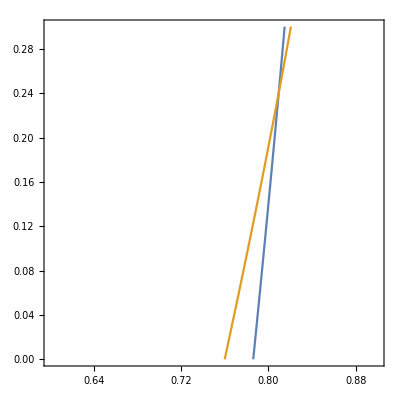

```mathematica
ContourPlot[{λmax==1,λmax2==1},{q1,0.6,0.9},{α,0,.3}]
```

```mathematica
λmax/.{q1->4/5}
```

2 (1/5+√(9/125+(16 α)/125))

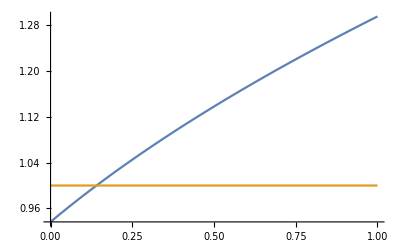

```mathematica
Plot[{λmax/.{q1->4/5},1},{α,0,1}]
```

```mathematica
Table[{α,λmax/.{q1->4/5}},{α,0.1,0.2,0.01}]
```

{{0.1,0.982409},{0.11,0.986788},{0.12,0.991135},{0.13,0.995449},{0.14,0.999733},{0.15,1.00399},{0.16,1.00821},{0.17,1.01241},{0.18,1.01657},{0.19,1.02071},{0.2,1.02482}}

```mathematica
eqn=Expand[λmax/.{q1->4/5}]
```

2/5+2 √(9/125+(16 α)/125)

```mathematica
TeXForm[eqn]
```

2 \sqrt{\frac{16 \alpha }{125}+\frac{9}{125}}+\frac{2}{5}

```mathematica
Solve[eqn==1,α]
```

```mathematica
N[{{α->9/64}}]
```

{{α→0.140625}}

```mathematica
9/64//TeXForm
```

\frac{9}{64}